```mathematica
SetDirectory[NotebookDirectory[]];
```

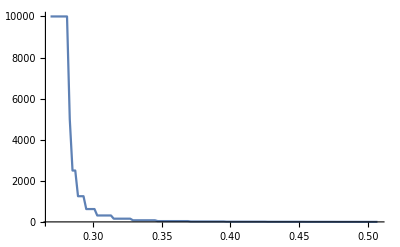

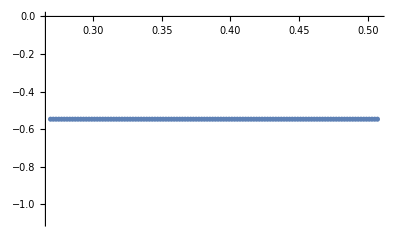

```mathematica
data=Import["./data.dat"];
rList=data[[All,1]];
cList=data[[All,2]];
eList=data[[All,3]];

rcPlot=ListLinePlot[Transpose@{rList,cList},PlotRange->All]
rePlot=ListPlot[Transpose@{rList,eList},PlotRange->All]
```

C has a “cut-off” property; what I means here is that for a given value of R, when C is lower than C_cutoff, it doesn’t change the corresponding bound state energy, which is around -0.5(-13.5eV) here. (data stops collecting up to R=0.267, since root can no longer be found between C=10000 to 20000.)